```mathematica
SetDirectory[NotebookDirectory[]];
var[data_]:=Block[{res,mean},
mean = Mean[data];
Sum[(data[[i]]-mean)^2,{i,1,Length[data]}]/(Length[data]-1)
]
```

```mathematica
data = Import["benchmark.csv"];
```

```mathematica
count[n_]:=Block[{filtered,cnot,depth},
filtered= Select[data,#[[1]]==n&];
{cnot,depth}={#2&@@@filtered,#3&@@@filtered};
{{Mean[cnot],Sqrt[var[cnot]]},{Mean[depth], Sqrt[var[depth]]}}//N
]
cnotedison = Around[#1,#2]&@@@Table[(count[n])[[1]],{n,5,20,5}];
```

```mathematica
(* ewout data *)
ewout = {{5,4,6}, {10,14,16},{15,32,31},{20,56,47}};
```

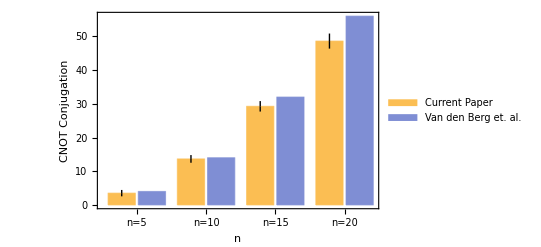

```mathematica
barchart = BarChart[Table[{cnotedison[[j]],ewout[[j,2]]},{j,1,Length[cnotedison]}],Frame->True,ChartLabels->{{"n=5","n=10","n=15","n=20"},None},ChartLegends->{"Current Paper","Van den Berg \net. al."},FrameLabel->{"n","CNOT Conjugation"}]
```

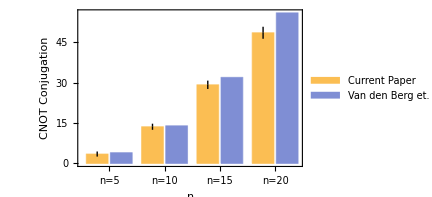

```mathematica
barchart2=Magnify[Show[barchart,AxesStyle->Directive[AbsoluteThickness[0.1],20,FontFamily->"Courier"],ImageSize->320],2]
```

```mathematica
Table[count[n],{n,5,20,5}][[1]]
```

{{3.5,0.945905},{8.5,2.18849}}

```mathematica
cnotedison = Export["../quantum-journal-5.0/cnotedison.csv",{#1,#2}&@@@Table[(count[n])[[1]],{n,5,20,5}]]
```

../quantum-journal-5.0/cnotedison.csv